# Equilibrium points of Rossler chaotic system

```mathematica
(*Rossler system *)
Rossler = {x'[t] == -(y[t]+z[t]), y'[t]==x[t]+a4*y[t], z'[t]==z[t](x[t]-c4)+b4 };
```

```mathematica
(*System parameters*)
a4 = 1/5; b4=1/5; c4=57/10;
```

```mathematica
(*Find the quilibrium points*)
{x,y,z}/.Solve[Thread[(Last/@Rossler/.a_[t]:>a)=={0,0,0}],{x,y,z}]
```

{{4/(5 (57+√3233)),4/(-57-√3233),4/(57+√3233)},{1/20 (57+√3233),1/4 (-57-√3233),1/4 (57+√3233)}}

```mathematica
N[{x,y,z}/.Solve[Thread[(Last/@Rossler/.a_[t]:>a)=={0,0,0}],{x,y,z}]]
```

{{0.0070262,-0.035131,0.035131},{5.69297,-28.4649,28.4649}}

## Jacobian Matrix

```mathematica
JacobianMatrix= Outer[D,{-(y+z),x+a4*y,z(x-c4)+b4 },{x,y,z}];
%//MatrixForm
```

(0 | -1 | -1
1 | 1/5 | 0
z | 0 | -57/10+x)

```mathematica
EigVa1 =Eigenvalues[JacobianMatrix/.{x->4/(5 (57+√3233)),y->4/(-57-√3233),z->4/(57+√3233)}]
Plot1=ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@ EigVa1,AspectRatio->1,PlotStyle->{Red, PointSize[Large]}];
```

{(Root-6.48 × 10^3Root[{-3233+#1^2&,4196434000+73803600 #1-67036 #2-1180 #1 #2+3127 #2^2+55 #1 #2^2+#2^3&},{2,1}]-6475.160507410643)/(10 (57+√3233)),(Root110.+1.13 × 10^3 ⅈRoot[{-3233+#1^2&,4196434000+73803600 #1-67036 #2-1180 #1 #2+3127 #2^2+55 #1 #2^2+#2^3&},{2,3}]110.44466636407631)/(10 (57+√3233)),(Root110.-1.13 × 10^3 ⅈRoot[{-3233+#1^2&,4196434000+73803600 #1-67036 #2-1180 #1 #2+3127 #2^2+55 #1 #2^2+#2^3&},{2,2}]110.44466636407631)/(10 (57+√3233))}

```mathematica
N[EigVa1]
```

{-5.68698,0.0970009+0.995193 ⅈ,0.0970009-0.995193 ⅈ}

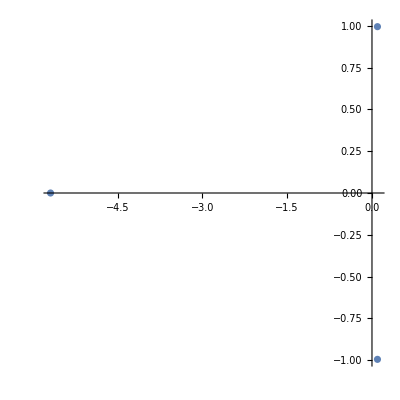

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@EigVa1,AspectRatio->1]
```

```mathematica
EigVa2 =
Eigenvalues[JacobianMatrix/.{x->1/20 (57+√3233),y->1/4 (-57-√3233),z->1/4 (57+√3233)}]
Plot2=ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@ EigVa1,
AspectRatio->1,PlotStyle->{Red, PointSize[Large]}];
```

{1/20 Root-9.19 × 10^-5+109. ⅈRoot[{-3233+#1^2&,-800 #1+5872 #2+104 #1 #2+53 #2^2-#1 #2^2+#2^3&},{2,3}]-0.00009192142077659204,1/20 Root-9.19 × 10^-5-109. ⅈRoot[{-3233+#1^2&,-800 #1+5872 #2+104 #1 #2+53 #2^2-#1 #2^2+#2^3&},{2,2}]-0.00009192142077659204,1/20 Root3.86Root[{-3233+#1^2&,-800 #1+5872 #2+104 #1 #2+53 #2^2-#1 #2^2+#2^3&},{2,1}]3.8596597461595508}

```mathematica
N[EigVa2]
```

{-4.59607×10^-6+5.42803 ⅈ,-4.59607×10^-6-5.42803 ⅈ,0.192983}

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@EigVa1,AspectRatio->1]
```

-Graphics-

### Evaluation of Jacobian matrix in equilibrium points

```mathematica
(*First equilibrium point*)
```

```mathematica
JacobianMatrix/.{x->4/(5 (57+√3233)),y->4/(-57-√3233),z->4/(57+√3233)}
```

{{0,-1,-1},{1,1/5,0},{4/(57+√3233),0,-57/10+4/(5 (57+√3233))}}

```mathematica
MatrixForm[N[JacobianMatrix/.{x->4/(5 (57+√3233)),y->4/(-57-√3233),z->4/(57+√3233)}]]
```

(0. | -1. | -1.
1. | 0.2 | 0.
0.035131 | 0. | -5.69297)

```mathematica
(*Second equilibrium point*)
```

```mathematica
JacobianMatrix/.{x->1/20 (57+√3233),y->1/4 (-57-√3233),z->1/4 (57+√3233)}
```

{{0,-1,-1},{1,1/5,0},{1/4 (57+√3233),0,-57/10+1/20 (57+√3233)}}

```mathematica
MatrixForm[N[JacobianMatrix/.{x->1/20 (57+√3233),y->1/4 (-57-√3233),z->1/4 (57+√3233)}]]
```

(0. | -1. | -1.
1. | 0.2 | 0.
28.4649 | 0. | -0.0070262)